## functions

```mathematica
SortedPositions[list_]:=Reverse[SortBy[Transpose[{Range[Length[list]],list}],#[[2]]&]]
```

```mathematica
RemapRange[value_,start1_,stop1_,start2_,stop2_]:=start2+(stop2-start2)((value-start1)/(stop1-start1))
```

## data

### transform

```mathematica
imageNames=FileNames[All,NotebookDirectory[]<>"production\\daily_images"];
images=Map[ImageData[Import[#]]&,imageNames];
productionData=Table[
Module[
{image,imageWidth,imageHeight,curvePixel,xStartPixel,xEndPixel,yStartPixel,yEndPixel,dateStamp,yMax,dailyYield,curvePixels,remappedPoints,powerData},
image=images[[imageN]];
imageWidth=Dimensions[image][[2]];
imageHeight=Dimensions[image][[1]];
curvePixel={0.09411764705882353,0.8117647058823529,0.5294117647058824,1.};xStartPixel=SortedPositions[Map[Total[Flatten[#]]&,Transpose[image]][[40;;80]]][[1]][[1]]+40;
xEndPixel=803;
yEndPixel=257;
dateStamp=StringSplit[StringDrop[StringSplit[imageNames[[imageN]],"\\"][[-1]],-4],"_"][[1]];
yMax=ToExpression[StringSplit[StringDrop[StringSplit[imageNames[[imageN]],"\\"][[-1]],-4],"_"][[2]]];
dailyYield=ToExpression[StringSplit[StringDrop[StringSplit[imageNames[[imageN]],"\\"][[-1]],-4],"_"][[3]]];
curvePixels=Position[Transpose[Reverse[image][[1;;yEndPixel]]],curvePixel];
yStartPixel=Min[Transpose[curvePixels][[2]]];
remappedPoints=Map[
{
RemapRange[#[[1]],xStartPixel,imageWidth,0,24 60 -5],
RemapRange[#[[2]],yStartPixel,yEndPixel,0,yMax]
}
&,curvePixels
];
powerData=Table[
Select[remappedPoints,Between[#[[1]],{minute-1,minute+1}]&]//If[#=={},{minute,0},Mean[#]]&
,{minute,0,24 60-5,5}];
{
dateStamp,
powerData,
dailyYield
}
]
,{imageN,1,Length[images]}];
```

```mathematica
Export[NotebookDirectory[]<>"production\\productionData.mx",productionData]
```

C:\Users\Beno\Documents\SZAKI\napelem\production\productionData.mx

### load & set

```mathematica
simulatedCapacity=33.6;
```

```mathematica
simulatedPerformance=Import[NotebookDirectory[]<>"simulation.csv"];
```

```mathematica
installedCapacity=36.08;
```

```mathematica
productionData=Import[NotebookDirectory[]<>"production\\productionData.mx"];
```

```mathematica
capacityCorrection=installedCapacity/simulatedCapacity;
```

## calc & analyse

```mathematica
month=1;
monthlyYieldSimulated=1000simulatedPerformance[[month+2]][[-3]]
dailyYieldSimulated=monthlyYieldSimulated/30
```

961.

32.0333

```mathematica
Mean[100Map[Last,productionData]/(dailyYieldSimulated capacityCorrection)]
```

52.7518

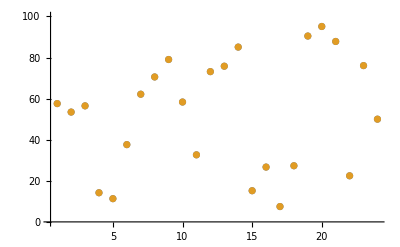

```mathematica
ListPlot[
{
100Map[Last,productionData]/(dailyYieldSimulated capacityCorrection),
100(Map[Last,productionData]/installedCapacity)/(monthlyYieldSimulated/simulatedCapacity/30)
}
,PlotRange->{All,{0,100}}]
```

```mathematica
allData=Flatten[Map[#[[2]]&,productionData],1];
```

```mathematica
binStep=5;
binWidth=45;
meanProduction=Table[
Flatten[{
minute,
Module[
{selectedData},
selectedData=Select[
allData,
Between[#[[1]],{minute-binWidth/2,minute+binWidth/2}]&
];
If[
selectedData=={},
{0,0},
GetMeanAndSEM[Transpose[selectedData][[2]]]
]
]
}]//If[Length[#]==3,#,Flatten[{#,0}]]&
,{minute,binStep,24 60-binStep-5,binStep}];
```

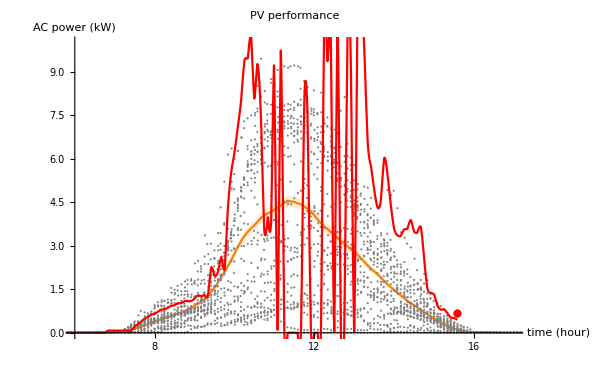

```mathematica
dayStart=6;
dayEnd=17;
dayLatestDataPointPos=
If[
60DateList[][[4]]+DateList[][[5]]>60 dayEnd,
(60 24)/5,
Range[0,24 60-5,5][[Max[Position[Sign[Differences[Transpose[productionData[[-1]][[2]]][[2]]]],-1]]]]/5+1
];
pvProductionPlot=Show[{
ErrorListPlot[
{Transpose[meanProduction]},
{Orange},
{
PlotRange->{{dayStart 60,dayEnd 60},{0,10}},
Ticks->{Map[{#,Floor[#/60]}&,Range[0,24 60,60]],Automatic},
AxesOrigin->{dayStart 60,0},
AxesLabel->{"time\n(hour)","AC power\n(kW)"},
PlotLabel->"PV performance"
},
{True,True,False}
],
ListPlot[
allData,PlotStyle->{{PointSize->0.0025,Gray}}],
(*Plot[
Map[Evaluate[Interpolation[#[[2]]]][x]&,productionData[[{-5,-2}]]],{x,0,24 60},PlotStyle->{{RGBColor[1,0,0,0.5]}},PlotRange->All
],*)
Plot[
Map[Evaluate[Interpolation[#[[2]]]][x]&,productionData[[{-3}]]],{x,0,(dayLatestDataPointPos-1)5},PlotStyle->Red,PlotRange->All
],
Graphics[
{Red,PointSize->0.01,Point[productionData[[-1]][[2]][[dayLatestDataPointPos]]]}
]
},ImageSize->600,AspectRatio->1/GoldenRatio]
```

```mathematica
Export[NotebookDirectory[]<>"pvProduction.png",pvProductionPlot]
```

C:\Users\Beno\Documents\SZAKI\napelem\pvProduction.png

```mathematica
productionInterpolated=Map[Evaluate[Interpolation[MovingAverage[#[[2]],30]]][x]&,productionData];
```

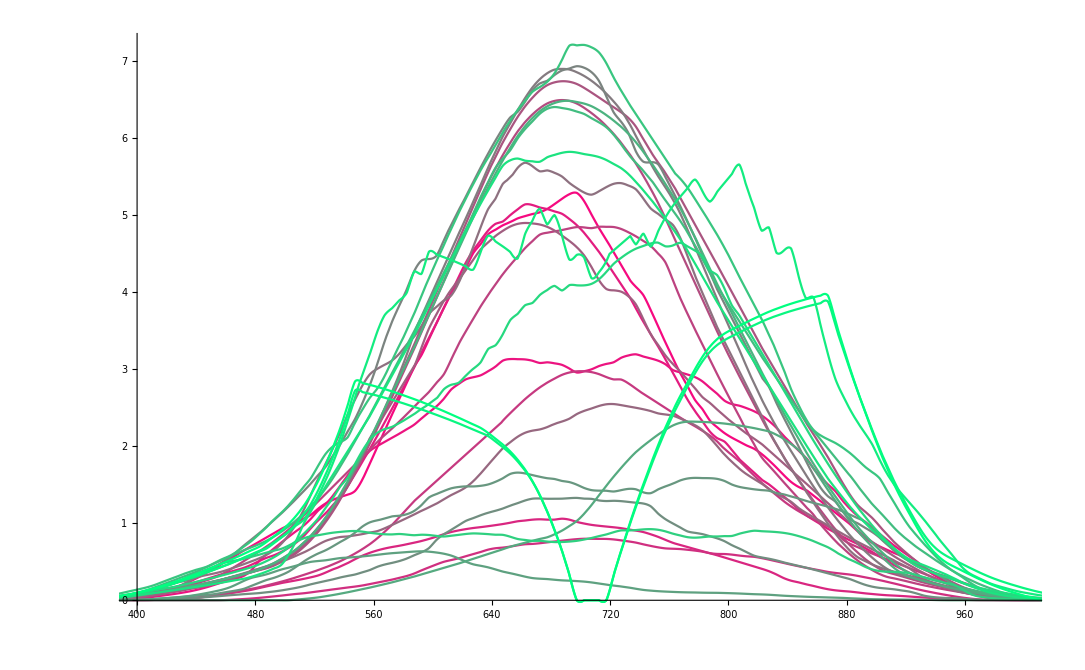

```mathematica
Quiet[Plot[
productionInterpolated,{x,0,24 60},PlotStyle->Table[RGBColor[1-n/Length[productionData],n/Length[productionData],0.5],{n,1,Length[productionData]}],PlotRange->{{400,1000},All}
]]
```

```mathematica
minuteStep=5;
kWStep=0.25;
minuteWindow=30;
kWWindow=2;
heatmap=Table[Table[
Length[Select[
allData,
Between[#[[1]],{minute-minuteWindow/2,minute+minuteWindow/2}]&&
Between[#[[2]],{kW-kWWindow/2,kW+kWWindow/2}]&
]]
,{kW,0,10,kWStep}]
,{minute,0,24 60-5,minuteStep}];
```

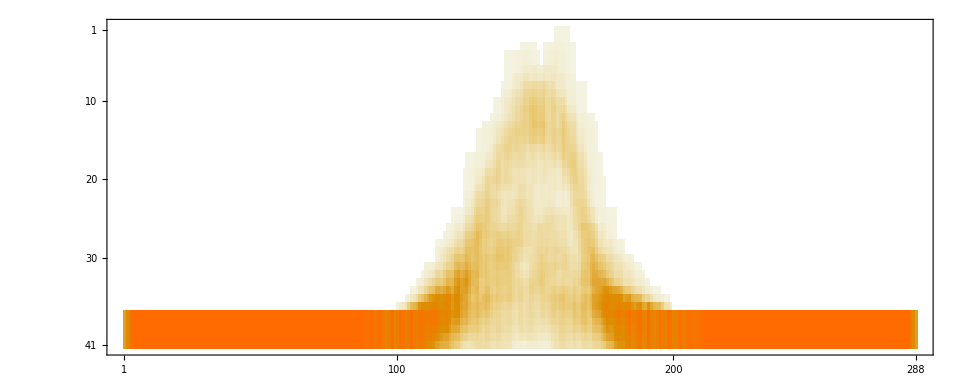

```mathematica
MatrixPlot[Reverse[Transpose[Reverse[heatmap]]]]
```

{28.7,0.945313}

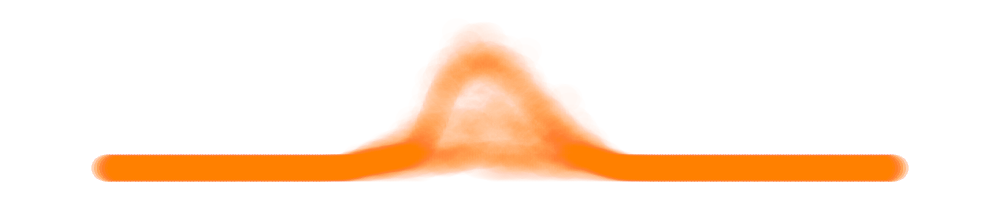

```mathematica
aspectRatio=5;
pointSize=0.1;
pointSizes={
pointSize(Max[Transpose[allData][[1]]]-Min[Transpose[allData][[1]]])/aspectRatio,
pointSize(Max[Transpose[allData][[2]]]-Min[Transpose[allData][[2]]])
}
Graphics[
Map[
{
RGBColor[1,0.5,0,0.01],
Ellipsoid[
{#[[1]],#[[2]]},
pointSizes
]
}&,allData],
ImageSize->1000,
AspectRatio->1/aspectRatio
]
```

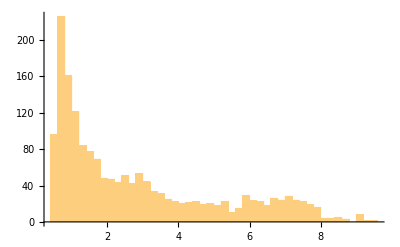

```mathematica
Histogram[Select[Transpose[allData][[2]],0.5<#&],50]
```

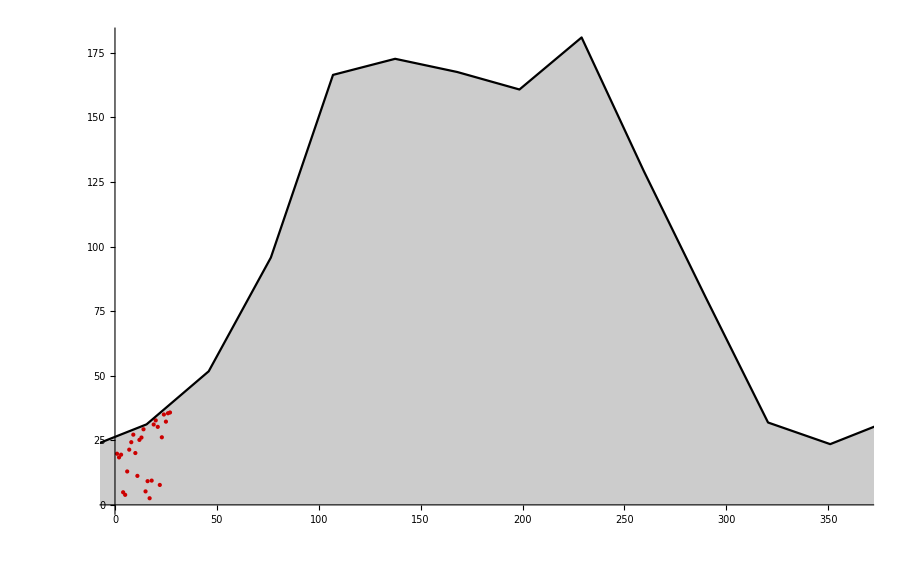

```mathematica
simulatedMonthlyProduction=Transpose[{Range[12]30.5-15,1000Transpose[capacityCorrection simulatedPerformance[[2+1;;2+12]]][[-2]]/30}];
ListPlot[
Join[
{{simulatedMonthlyProduction[[12]][[1]]-360,simulatedMonthlyProduction[[12]][[2]]}},
simulatedMonthlyProduction,
{{simulatedMonthlyProduction[[1]][[1]]+360,simulatedMonthlyProduction[[1]][[2]]}}
],PlotRange->{{0,365},All},
Prolog->Map[{Red,Point[#]}&,Transpose[{Range[Length[images]],Map[Last,productionData]}]],PlotStyle->Black,Joined->True,Filling->Axis
]
```

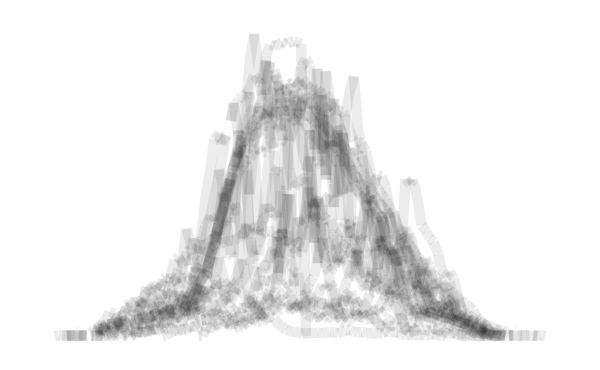

```mathematica
timeRes=1;
powerRes=0.01;
allTransitions=GatherBy[
Map[
Module[
{new},
new={
{Round[#[[1]][[1]]/timeRes],Round[#[[1]][[2]],powerRes]},
{Round[#[[2]][[1]]/timeRes],Round[#[[2]][[2]],powerRes]}
};
If[
N[new[[1]][[2]]]==N[new[[2]][[2]]]==0.,
Nothing,
new
]
]
&,Flatten[Table[
Drop[Transpose[{dayData[[2]],RotateLeft[dayData[[2]]]}],-1]
,{dayData,productionData}],1]],
#[[1]]&];
Graphics[
Table[
Module[
 {assoc,totalWeights,maxWeight},
assoc=Counts[transitionData];
totalWeights=Total[KeyValueMap[#2&,assoc]];
maxWeight=Max[KeyValueMap[#2&,assoc]];
KeyValueMap[
{
Thickness->0.025-RemapRange[Power[#2/totalWeights,10],0,1,0,0.0125],
GrayLevel[0,Power[RemapRange[Power[#2/totalWeights,10],0,1,0,0.075],1]],
Line[#1]
} 
&,Reverse[KeySortBy[assoc,assoc[#]&]][[1;;Min[10,Length[assoc]]]]]
]
,{transitionData,allTransitions}],
ImageSize->600,AspectRatio->1/GoldenRatio
]
```

## dev

### I-V curve

```mathematica
img=Import[NotebookDirectory[]<>"I-V curve\\test.png"];
```

```mathematica
img
```

-Graphics-

```mathematica
vCol=ImageData[img][[27]][[67]]
```

{0.360784,0.796078,0.694118,1.}

```mathematica
iCol=ImageData[img][[27]][[250]]
```

{0.305882,0.686275,0.960784,1.}

```mathematica
xPlotRange={94,1425};
yPlotRange={76,520};
```

```mathematica
vMax=800;
iMax=3.5;
```

```mathematica
vPixels=Map[
{
RemapRange[#[[1]],xPlotRange[[1]],xPlotRange[[2]],0,24 60 -5],
RemapRange[#[[2]],yPlotRange[[1]],yPlotRange[[2]],0,vMax]
}
&,
Select[
Position[Transpose[Reverse[ImageData[img]]],vCol],
Between[#[[1]],xPlotRange]&&Between[#[[2]],yPlotRange]
&
]];
vData=Table[
Select[vPixels,Between[#[[1]],{minute-1,minute+1}]&]//If[#=={},{minute,0},{minute,Mean[Transpose[#][[2]]]}]&
,{minute,0,24 60 -5,5}];
```

```mathematica
iPixels=Map[
{
RemapRange[#[[1]],xPlotRange[[1]],xPlotRange[[2]],0,24 60 -5],
RemapRange[#[[2]],yPlotRange[[1]],yPlotRange[[2]],0,iMax]
}
&,
Select[
Position[Transpose[Reverse[ImageData[img]]],iCol],
Between[#[[1]],xPlotRange]&&
Between[#[[2]],yPlotRange]
&
]];
iData=Table[
Select[iPixels,Between[#[[1]],{minute-1,minute+1}]&]//If[#=={},{minute,0},{minute,Mean[Transpose[#][[2]]]}]&
,{minute,0,24 60 -5,5}];
```

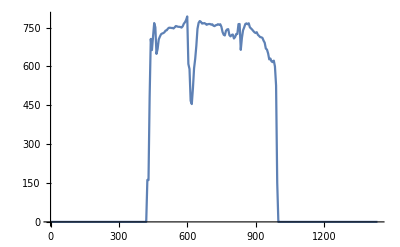

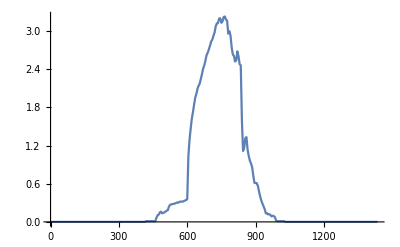

```mathematica
ListPlot[vData,Joined->True]
ListPlot[iData,Joined->True]
```

```mathematica
vData//Dimensions
```

{288,2}

```mathematica
iData//Dimensions
```

{288,2}

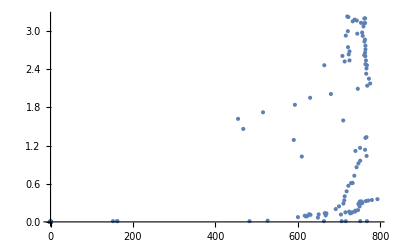

```mathematica
ListPlot[
Transpose[{Transpose[vData][[2]],Transpose[iData][[2]]}]
]
```

```mathematica
alma=Import["C:\\Users\\Beno\\Documents\\SZAKI\\napelem\\production\\Inverter_INV-6T2199057504_20240202115641\\his_inv_rd"];
```

```mathematica
alma
```

{his_inv_rd}

### lemosás

```mathematica
monthLengths={31,28,31,30,31,30,31,31,30,31,30,31};
```

```mathematica
monthNames={"Jan","Feb","Márc","Ápr","Máj","Jún","Júl","Aug","Szept","Okt","Nov","Dec"};
```

```mathematica
simulatedDailyProduction=Table[
{
DateDifference[DateObject[{2024,1,1}],DateObject[{2024,month,monthLengths[[month]]/2}]][[1]]+1,
(1000Transpose[simulatedPerformance][[-2]][[2+1;;2+12]]capacityCorrection)[[month]]/monthLengths[[month]]
}
,{month,1,12}];
```

```mathematica
Export[NotebookDirectory[]<>"termeles.csv",Transpose[{monthNames,0.63 1000Transpose[simulatedPerformance][[-2]][[2+1;;2+12]]capacityCorrection}]]
```

C:\Users\Beno\Documents\SZAKI\napelem\termeles.csv

```mathematica
idioticCorrection=1/0.68;
idioticCorrection=1;
```

```mathematica
dailyProduction=Transpose[
{
Range[Length[ToExpression[StringSplit[Import[NotebookDirectory[]<>"production\\days.txt"],"\n"]]/100]],idioticCorrection ToExpression[StringSplit[Import[NotebookDirectory[]<>"production\\days.txt"],"\n"]]/100
}];
```

```mathematica
dailyProduction//N
```

{{1.,0.},{2.,1.67},{3.,19.81},{4.,18.39},{5.,19.43},{6.,4.88},{7.,3.89},{8.,12.49},{9.,21.38},{10.,24.27},{11.,27.19},{12.,20.07},{13.,11.23},{14.,25.16},{15.,26.08},{16.,29.27},{17.,5.22},{18.,9.18},{19.,2.57},{20.,9.4},{21.,31.12},{22.,32.72},{23.,30.21},{24.,7.72},{25.,26.17},{26.,34.99},{27.,32.23},{28.,35.47},{29.,35.9},{30.,35.02},{31.,31.29},{32.,20.53},{33.,33.17},{34.,25.57},{35.,28.95},{36.,39.73},{37.,39.28},{38.,38.52},{39.,45.83},{40.,20.39},{41.,41.06},{42.,19.82},{43.,17.01},{44.,47.26},{45.,48.5},{46.,28.14},{47.,51.02},{48.,41.53},{49.,40.5},{50.,18.72},{51.,51.06},{52.,39.11},{53.,37.53},{54.,12.42},{55.,34.93},{56.,32.52},{57.,46.71},{58.,57.56},{59.,55.58},{60.,50.99},{61.,24.27},{62.,9.97},{63.,64.65},{64.,65.07},{65.,65.55},{66.,53.53},{67.,17.86},{68.,19.61},{69.,64.24},{70.,46.18},{71.,25.82},{72.,24.47},{73.,52.19},{74.,80.94},{75.,76.5},{76.,52.46},{77.,91.02},{78.,92.25},{79.,76.36},{80.,90.47},{81.,84.47},{82.,61.01},{83.,63.31},{84.,79.28},{85.,59.57},{86.,93.81},{87.,66.44},{88.,91.67},{89.,75.79},{90.,93.51},{91.,83.45},{92.,91.04},{93.,72.9},{94.,101.68},{95.,74.81},{96.,124.54},{97.,103.2},{98.,136.1},{99.,135.89},{100.,131.72},{101.,127.52},{102.,130.}}

```mathematica
Mean[Map[
#[[2]]/Quiet[Interpolation[simulatedDailyProduction,InterpolationOrder->1][#[[1]]]]
&,dailyProduction
]]
```

0.645151

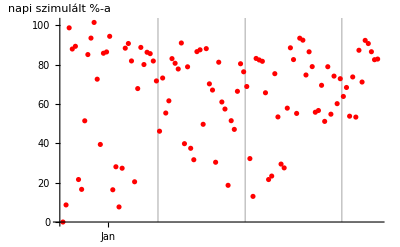

```mathematica
arany=ListPlot[Map[
#[[2]]/Quiet[Interpolation[simulatedDailyProduction,InterpolationOrder->1][#[[1]]]]
&,dailyProduction
],PlotStyle->Red,AxesLabel->{None,"napi szimulált %-a"},ImageSize->400,
Ticks->{
Table[{Accumulate[monthLengths][[month]]-monthLengths[[month]]/2,monthNames[[month]]},{month,1,12}],Transpose[{Range[0,1,0.2],Round[100Range[0,1,0.2]]}]
},
Prolog->{RGBColor[0,0,0,0.25],Table[Line[{{month+0.5,0},{month+0.5,200}}],{month,Accumulate[monthLengths]}]}
]
```

```mathematica
Export[NotebookDirectory[]<>"relativ.png",arany]
```

C:\Users\Beno\Documents\SZAKI\napelem\relativ.png

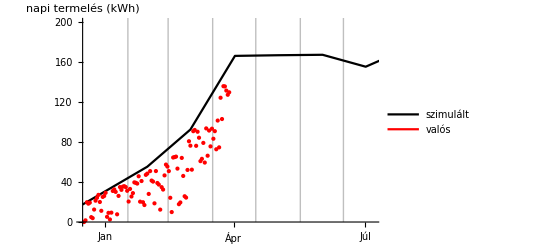

```mathematica
tenyEsTerv=ListPlot[
{
Table[Quiet[{day,Interpolation[simulatedDailyProduction,InterpolationOrder->1][day]}],{day,0,365}],
 dailyProduction,
{{-10,10}}
},PlotRange->{{0,dailyProduction[[-1]][[1]]+100},{0,200}},Joined->{True,False,True},PlotStyle->{{Thick,Black},{PointSize->0.01,Red},Red},ImageSize->400,AxesLabel->{None,"napi termelés\n(kWh)"},
Ticks->{
Table[{Accumulate[monthLengths][[month]]-monthLengths[[month]]/2,monthNames[[month]]},{month,1,12}],
Automatic
},
Prolog->{RGBColor[0,0,0,0.25],Table[Line[{{month+0.5,0},{month+0.5,300}}],{month,Accumulate[monthLengths]}]},
PlotLegends->Placed[{"szimulált",None,"valós"},Bottom]
]
```

```mathematica
Export[NotebookDirectory[]<>"abszolut.png",tenyEsTerv]
```

C:\Users\Beno\Documents\SZAKI\napelem\abszolut.png

```mathematica
Interpolation[simulatedDailyProduction,InterpolationOrder->1][dailyProduction[[-1]][[1]]]
```

156.952

```mathematica
dailyProduction[[dailyProduction[[-1]][[1]]]][[2]]/Interpolation[simulatedDailyProduction,InterpolationOrder->1][dailyProduction[[-1]][[1]]]
```

0.828281

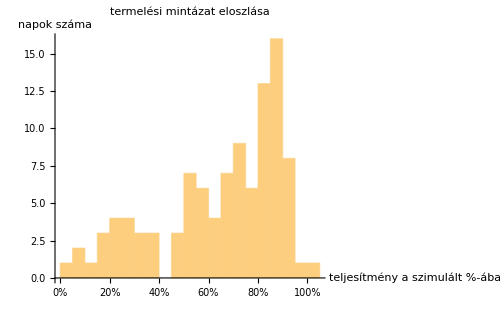

```mathematica
eloszlas=Histogram[
Map[
#[[2]]/Quiet[Interpolation[simulatedDailyProduction,InterpolationOrder->1][#[[1]]]]
&,dailyProduction
],25,
AxesLabel->{"teljesítmény a\nszimulált %-ában","napok száma"},
Ticks->{Map[{#,ToString[Round[100#]]<>"%"}&,Range[0,1,0.2]],Automatic},ImageSize->500,
PlotLabel->"termelési mintázat eloszlása"
]
```

```mathematica
Export[NotebookDirectory[]<>"eloszlas.png",eloszlas]
```

C:\Users\Beno\Documents\SZAKI\napelem\eloszlas.png

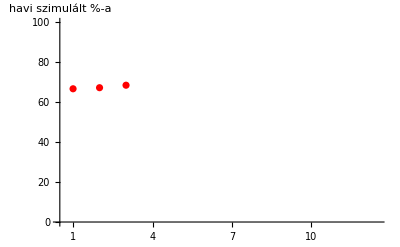

```mathematica
ListPlot[
Table[
N[Total[Transpose[dailyProduction][[2]][[
If[month==1,1,Accumulate[monthLengths][[month-1]]];;
Accumulate[monthLengths][[month]]
]]]]/(1000Transpose[simulatedPerformance][[-2]][[2+1;;2+12]]capacityCorrection)[[month]]
,{month,1,3}],
PlotStyle->Red,AxesLabel->{None,"havi szimulált %-a"},ImageSize->400,
Ticks->{
Range[12],Transpose[{Range[0,1,0.2],Round[100Range[0,1,0.2]]}]
},PlotRange->{{0.5,12.5},{0,1}}
]
```

```mathematica
Table[N[Total[Transpose[dailyProduction][[2]][[
If[month==1,1,Accumulate[monthLengths][[month-1]]];;
Accumulate[monthLengths][[month]]
]]]],{month,1,3}]//Total
```

5349.26

```mathematica
Table[N[Total[Transpose[dailyProduction][[2]][[
If[month==1,1,Accumulate[monthLengths][[month-1]]];;
Accumulate[monthLengths][[month]]
]]]],{month,1,3}]//Total//(#/0.68)-#&
```

1711.76

```mathematica
1/0.68
```

1.47059

### E.On

```mathematica
eonData=Map[StringSplit[#,";"][[1]]&,Import[NotebookDirectory[]<>"eon_01102023_22032024.csv"]];
```

```mathematica
eonFelvett=Select[eonData,#[[2]]=="'+A'"&];
eonLeadott=Select[eonData,#[[2]]=="'-A'"&];
```

```mathematica
eonData[[1]]
```

{POD név,Változó név,Idő,Érték [kWh],Státusz}

```mathematica
Map[#[[3]]&,eonFelvett]
```

{2023.10.01 00:15:00,2023.10.01 00:30:00,2023.10.01 00:45:00,2023.10.01 01:00:00,2023.10.01 01:15:00,2023.10.01 01:30:00,2023.10.01 01:45:00,2023.10.01 02:00:00,2023.10.01 02:15:00,2023.10.01 02:30:00,2023.10.01 02:45:00,2023.10.01 03:00:00,16589,2024.03.21 21:30:00,2024.03.21 21:45:00,2024.03.21 22:00:00,2024.03.21 22:15:00,2024.03.21 22:30:00,2024.03.21 22:45:00,2024.03.21 23:00:00,2024.03.21 23:15:00,2024.03.21 23:30:00,2024.03.21 23:45:00,2024.03.22 00:00:00}
 |  |  |  |

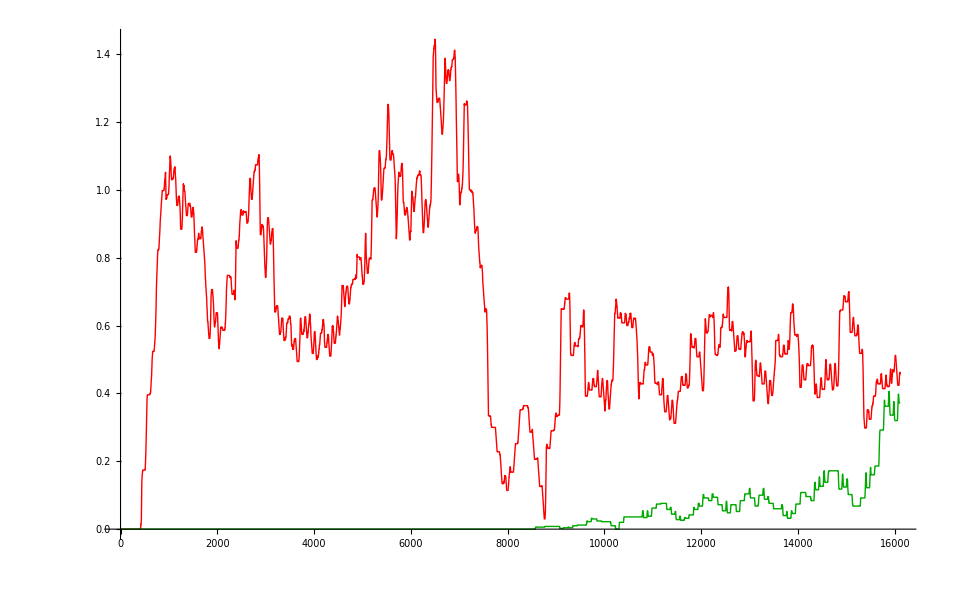

```mathematica
ListPlot[{
MovingAverage[ToExpression[Map[#[[4]]&,eonFelvett]],500],
MovingAverage[ToExpression[Map[#[[4]]&,eonLeadott]],500]
},Joined->True,PlotStyle->{{Thick,Red},{Thick,Darker[Green]}},ImageSize->1000
]
```

### FusionSolar

```mathematica
fusionSolarData=ToExpression[StringSplit[Import[NotebookDirectory[]<>"production\\fusion_solar_extraction.txt"],"\n"]];
```

```mathematica
maybePV=Select[fusionSolarData,Between[#,{1,5000}]&];
```

```mathematica
positions=Map[Position[fusionSolarData,#]&,maybePV[[1;;100]]];
```

```mathematica
fusionSolarData[[Range[100]5]]
```

{0,0,0,0,0,0,0,0,0,0,5312,5312,0,0,0,0,0,0,0,0,0,0,0,32767,0,0,0,0,0,0,0,0,0,0,0,5312,5312,0,0,0,0,0,0,0,0,0,0,0,32767,0,0,0,0,0,0,0,0,0,0,0,5312,5312,0,0,0,0,0,0,0,0,0,0,0,32767,0,0,0,0,0,0,0,0,0,0,0,5374,5374,0,0,0,0,0,0,0,0,0,0,0,32767,0}

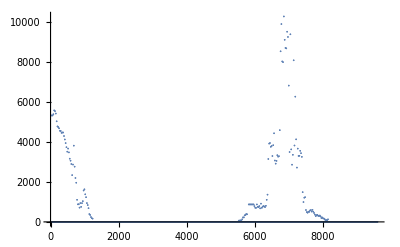

```mathematica
ListPlot[DeleteCases[fusionSolarData[[Range[10000]5]],32767]]
```